## V2

### Fix munging

And we can also ask, for example, how common different “oscillator primitives” are in building up other oscillators:

Fix munging

```mathematica
oresall = ;
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,GraphicsColumn[{ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[100],100}],$LifeData[#1]["Period"]}]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

```mathematica
oresall = ;
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,
ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[125],125}, Mesh->True,MeshStyle->Opacity[.1], Epilog->{FaceForm@Transparent, Rectangle[Scaled[{0, .25}], Scaled[{1, 1}]],Style[Text[$LifeData[#1]["Period"], Scaled[{.5,.25}]], 9]}, PlotRangePadding->{Automatic, Scaled/@{.45, 0}}, Frame->False]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

### Add pattern callout. Possibly add horizontal guides.

But after that, for nearly two decades, no more spaceships were found.  In 1989, however, a systematic method for searching was invented, and in the years since, a steady stream of new spaceships have been found.  A variety of different periods have been seen

Add pattern callout
Possibly add horizontal guides

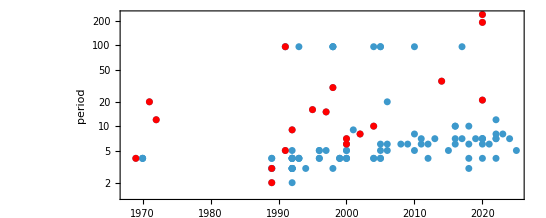

```mathematica
With[{data=Values[{#Year,#Period}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log"]]
```

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1,Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[RGBColor[0.24, 0.6, 0.8], PointSize[.01]], PlotRangePadding->{ {Automatic, 0}, Automatic}]
```

-Graphics-

Not right, bit of a challenge with the log scaling

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1,Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> RGBColor[0.24, 0.6, 0.8],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&])[[All, -1]]})

]
```

-Graphics-